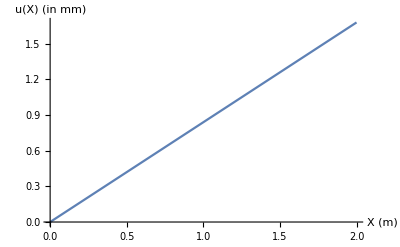

```mathematica
L=2; (*in m*)
α=12 10^-6; (*1/degree centigrade*)
Ε=1.0 10^11; (*in Pa*)
ΔT=80-10; (*in degree centigrade*)
δ=α ΔT L//N;
u[X_]:=α ΔT X
Plot[u[X] 10^3,{X,0,L},AxesLabel->{"X (m)","u(X) (in mm)"}]
```